## Part 1

I’m using data from a MESA (Modules for Experiments in Stellar Astrophysics) project I did a while ago. I tracked the stellar evolution of main sequence stars from 0.4 - 0.818 M_⊙.

```mathematica
mass={4,5,6,7,75,8,805,810,811,812,813,814,815,816,817,8175,81767,81783,8179,81795,818};
```

importHR imports the text files of the evolutionary tracks (in terms of log effective temperature and log luminosity) of the stars.

```mathematica
importHR=Table["dataHR"<>ToString[mass[[i]]]<>"=Import[\""<>NotebookDirectory[]<>"evolTracks/0."<>ToString[mass[[i]]]<>"M/hr.txt\",\"Table\"]",{i,Length[mass]}];
```

```mathematica
Do[ToExpression[importHR[[i]]],{i,Length[importHR]}]
```

I chose the 0.8179 M_⊙ stars track to use as the evolutionary track because it evolved the furthest before reaching helium burning.

```mathematica
HR8179M=ListPlot[dataHR8179,PlotRange->{{3.5,3.9},{-1.5,3.5}},Joined-> True,ScalingFunctions->{"Reverse",Identity},PlotStyle->{RGBColor[0.4,0,0.4],Dashed,Arrowheads[{0,.02,.02,0}]}]/.Line->Arrow;
```

The points I chose for the isochrone are the (logT, logL) points in each star’s evolutionary track at 12Gyr (~amount of time until 0.8179 M_⊙ star reached reached helium burning) .

```mathematica
isochronePts=Table[ToExpression["dataHR"<>ToString[mass[[i]]]][[Length[ToExpression["dataHR"<>ToString[mass[[i]]]]]]],{i,Length[mass]}];
```

```mathematica
isochrone=ListPlot[Table[isochronePts[[i]],
{i,Length[mass]-2}],ScalingFunctions->{"Reverse",Identity},PlotStyle->GrayLevel[0.67,0.85],Joined->True];
```

The isochrone should roughly match up with the evolutionary track.

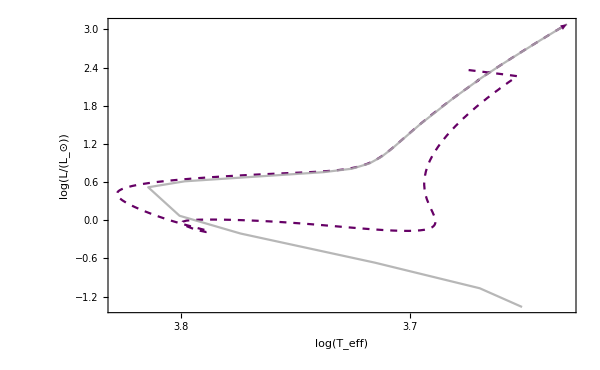

```mathematica
evolIsochrone=Show[HR8179M,isochrone,Frame-> True,FrameLabel-> {"log(T_eff)","log(L/(L_(<⊙>)))"},LabelStyle-> 14,ImageSize->600,Epilog->Inset[Framed[Column[{LineLegend[{Purple},{"Evolutionary Track"}],LineLegend[{GrayLevel[0.67,0.85]},{"Isochrone"}]}],RoundingRadius->1],ImageScaled[{0.8,0.4}],BaseStyle->10]]
```

## Part 2

```mathematica
SerCos[x_,n_]:=Normal[Series[Cos[x],{x,0,n}]]
SerSin[x_,n_]:=Normal[Series[Sin[x],{x,0,n}]]
```

```mathematica
nVal=10
```

10

```mathematica
sinDiff[x_]=SerSin[x,nVal]-Sin[x]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880-Sin[x]

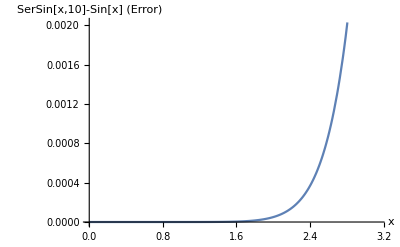

```mathematica
Plot[sinDiff[x],{x,0,π},AxesLabel->{"x","SerSin[x,"<>ToString[nVal]<>"]-Sin[x] (Error)"}]
```

```mathematica
sq[x_]=(SerCos[x,nVal])^2+(SerSin[x,nVal])^2
```

(x-x^3/6+x^5/120-x^7/5040+x^9/362880)^2+(1-x^2/2+x^4/24-x^6/720+x^8/40320-x^10/3628800)^2

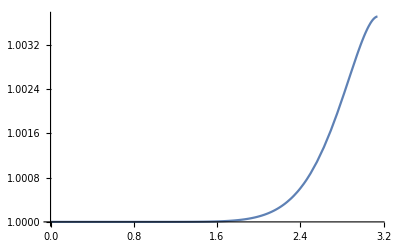

```mathematica
Plot[sq[x],{x,0,π},PlotRange->All]
```

What goes wrong, graphically and algebraically?

```mathematica
SerCosSq[x_,n_]:=Normal[Series[(Cos[x])^2,{x,0,n}]]
SerSinSq[x_,n_]:=Normal[Series[(Sin[x])^2,{x,0,n}]]
```

```mathematica
sqSer[x_]=SerCosSq[x,nVal]+SerSinSq[x,nVal]
```

1

## Part 3

#### Problem 1

```mathematica
rX[θ_]={{1,0,0},{0,Cos[θ],-Sin[θ]},{0,Sin[θ],Cos[θ]}};
rY[ζ_]={{Cos[ζ],0,Sin[ζ]},{0,1,0},{-Sin[ζ],0,Cos[ζ]}};
rZ[ϕ_]={{Cos[ϕ],-Sin[ϕ],0},{Sin[ϕ],Cos[ϕ],0},{0,0,1}};
```

```mathematica
rX[θ]//MatrixForm
rY[ζ]//MatrixForm
rZ[ϕ]//MatrixForm
```

(1 | 0 | 0
0 | Cos[θ] | -Sin[θ]
0 | Sin[θ] | Cos[θ])

(Cos[ζ] | 0 | Sin[ζ]
0 | 1 | 0
-Sin[ζ] | 0 | Cos[ζ])

(Cos[ϕ] | -Sin[ϕ] | 0
Sin[ϕ] | Cos[ϕ] | 0
0 | 0 | 1)

#### Problem 2

```mathematica
Rot3[ψ_,θ_,ϕ_]=rZ[ψ].rX[θ].rZ[ϕ];
```

```mathematica
Rot3[ψ,θ,ϕ]//MatrixForm
```

(Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ] | -Cos[ψ] Sin[ϕ]-Cos[θ] Cos[ϕ] Sin[ψ] | Sin[θ] Sin[ψ]
Cos[θ] Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[ψ] | Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ] | -Cos[ψ] Sin[θ]
Sin[θ] Sin[ϕ] | Cos[ϕ] Sin[θ] | Cos[θ])

#### Problem 3

```mathematica
Rot3Inverse[ψ_,θ_,ϕ_]=rZ[-ϕ].rX[-θ].rZ[-ψ];
```

```mathematica
Rot3Inverse[ψ,θ,ϕ]//MatrixForm
```

(Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ] | Cos[θ] Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[ψ] | Sin[θ] Sin[ϕ]
-Cos[ψ] Sin[ϕ]-Cos[θ] Cos[ϕ] Sin[ψ] | Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ] | Cos[ϕ] Sin[θ]
Sin[θ] Sin[ψ] | -Cos[ψ] Sin[θ] | Cos[θ])

```mathematica
(Simplify[Rot3Inverse[ψ,θ,ϕ].Rot3[ψ,θ,ϕ]])//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

#### Problem 4

```mathematica
rot3Inverse2[ψ_,θ_,ϕ_]=Simplify[Inverse[Rot3[ψ,θ,ϕ]]];
```

```mathematica
rot3Inverse2[ψ,θ,ϕ]//MatrixForm
```

(Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ] | Cos[θ] Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[ψ] | Sin[θ] Sin[ϕ]
-Cos[ψ] Sin[ϕ]-Cos[θ] Cos[ϕ] Sin[ψ] | Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ] | Cos[ϕ] Sin[θ]
Sin[θ] Sin[ψ] | -Cos[ψ] Sin[θ] | Cos[θ])

```mathematica
(Simplify[rot3Inverse2[ψ,θ,ϕ].Rot3[ψ,θ,ϕ]])//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
(Rot3Inverse[ψ,θ,ϕ]-rot3Inverse2[ψ,θ,ϕ])//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)